# Neural Networks

Use a GPU for training, when available:

```mathematica
SetOptions[NetTrain,TargetDevice->"GPU"];
```

### Classification of randomly distributed data

Create randomly distributed data (using the normal distribution):

```mathematica
sample[x_,n_]:=RandomVariate[NormalDistribution[x,1],n]
```

Get 10 samples:

```mathematica
sample[0,10]
```

{-0.116219,-0.0996973,-0.898734,-0.857998,-0.311289,-1.3269,-1.23411,0.941788,-0.326097,0.511952}

Create three clusters of data:

```mathematica
Manipulate[
clusters=sample[#,200]&/@{x,y,z};
NumberLinePlot[clusters,PlotRange->{-10,10}],
{x,-10,10},
{y,-10,10},
{z,-10,10}
]
```

Show them on the number line as individual clusters:

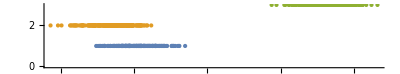

```mathematica
NumberLinePlot[clusters]
```

Set up the neural network with four layers. The first layer is fully connected (DotPlusLayer). The second layer is an elementwise layer which applies the Ramp function. The third layer is again fully connected and brings the nodes down to three. The Softmax layer helps to compute the probabilities of each label (“a”, “b”, or “c”):

```mathematica
net=NetChain[{
DotPlusLayer[30],
ElementwiseLayer[Ramp],
DotPlusLayer[3],
SoftmaxLayer[]
},
"Input"->"Scalar",
"Output"->NetDecoder[{"Class",{"a","b","c"}}]
]
```

NetChain[]

Set up the test data. We’re using the previously created “clusters”:

```mathematica
data=Join[
Thread[clusters[[1]]->"a"],
Thread[clusters[[2]]->"b"],
Thread[clusters[[3]]->"c"]
];
RandomSample[data,10]//Column[#,Alignment->"→"]&
```

5.79282→c
5.84401→c
9.26346→c
-5.08772→b
5.80337→c
-4.00508→a
-5.39183→b
-5.26916→b
-3.77954→a
7.19082→c

Train the neural network, with the NetTrain function:

```mathematica
result=NetTrain[net,data]
```

NetChain[]

Check the result:

```mathematica
Map[{#,result[#]}&,
{-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10}]
```

{{-10,b},{-9,b},{-8,b},{-7,b},{-6,b},{-5,b},{-4,a},{-3,a},{-2,a},{-1,a},{0,a},{1,a},{2,c},{3,c},{4,c},{5,c},{6,c},{7,c},{8,c},{9,c},{10,c}}

```mathematica
Map[<|
"input"->#,
"predicted"->result[#],
"probabilities"->result[#,"Probabilities"]
|>&,
Range[-10,10]
]//Dataset
```

Dataset[<>]

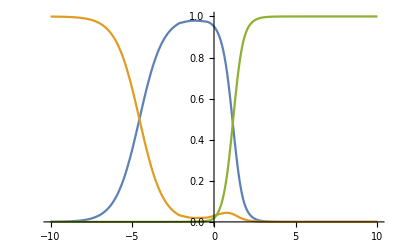

```mathematica
Plot[{
result[x,{"Probability","a"}],
result[x,{"Probability","b"}],
result[x,{"Probability","c"}]
},
{x,-10,10}
]
```

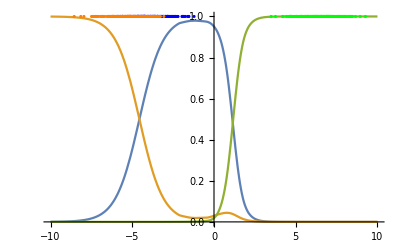

```mathematica
Show[
Plot[{
result[x,{"Probability","a"}],
result[x,{"Probability","b"}],
result[x,{"Probability","c"}]
},
{x,-10,10}
],
ListPlot[Map[{#,1}&,clusters,{2}],PlotStyle->{Blue,Orange,Green}]
]
```

### Classification of randomly distributed data (2)

```mathematica
sample[x_,n_]:=RandomVariate[NormalDistribution[x,1],n]
```

```mathematica
sample[0,10]
```

{1.03591,-0.538146,-2.00252,1.53879,-0.342824,-0.8388,-0.39311,0.0385012,-0.862505,-0.604017}

```mathematica
clusters=sample[#,200]&/@{-16,-10,-4,0,4,5,6};
```

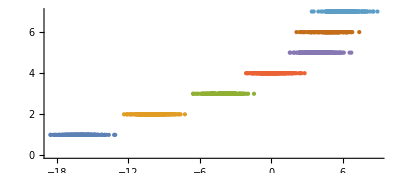

```mathematica
NumberLinePlot[clusters]
```

```mathematica
net=NetChain[{
DotPlusLayer[30],
ElementwiseLayer[Ramp],
DotPlusLayer[7],
SoftmaxLayer[]
},
"Input"->"Scalar",
"Output"->NetDecoder[{"Class",{"a","b","c","d","e","f","g"}}]
]
```

NetChain[]

```mathematica
data=Join@@MapThread[
Thread[#1->#2]&,
{clusters,{"a","b","c","d","e","f","g"}}];
RandomSample[data,10]//Column[#,Alignment->"→"]&
```

0.542379→d
-16.39→a
2.84016→e
-3.94803→c
2.33056→e
6.79993→g
-10.1417→b
-0.635897→d
-18.5298→a
0.0928981→d

```mathematica
result=NetTrain[net,data]
```

NetChain[]

```mathematica
result[0]
```

d

```mathematica
result[0,"Probabilities"]
```

<|a→4.57157×10^-10,b→0.0000425804,c→0.00197355,d→0.997749,e→0.000209344,f→0.0000251548,g→8.88907×10^-9|>

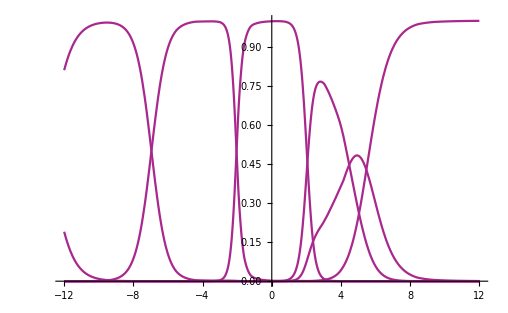

```mathematica
Plot[
Table[result[x,{"Probability",label}],{label,{"a","b","c","d","e","f","g"}}],
{x,-12,12},
PlotRange->All
]
```

### Classification of randomly distributed data (2 dimensions)

```mathematica
sample[c_,n_]:=RandomVariate[MultinormalDistribution[c,IdentityMatrix[2]],n]
```

```mathematica
sample[{0,0},10]//Grid
```

-1.19626 | -0.0709878
0.0699932 | -0.371723
0.0973565 | -1.72532
-0.165674 | -1.78007
0.191485 | -0.209326
-1.26905 | 1.17245
-0.659143 | 1.05835
-0.0730971 | -0.515734
-0.673797 | 1.23874
2.69979 | -0.0246831

```mathematica
clusters=sample[#,1000]&/@{{1.5,1},{-1.5,1},{0,-3}};
```

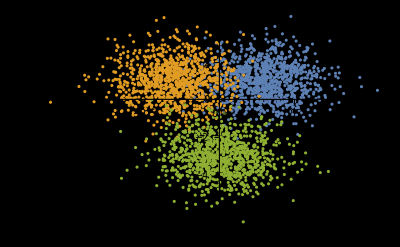

```mathematica
ListPlot[clusters,PlotTheme->"Minimal",Background->Black]
```

```mathematica
net=NetChain[{
DotPlusLayer[30],
ElementwiseLayer[Ramp],
DotPlusLayer[3],
SoftmaxLayer[]
},
"Input"->{2},
"Output"->NetDecoder[{"Class",{"cat","dog","goat"}}]
]
```

NetChain[]

```mathematica
data=Join[
Thread[clusters[[1]]->"cat"],
Thread[clusters[[2]]->"dog"],
Thread[clusters[[3]]->"goat"]
];
RandomSample[data,10]//Column[#,Alignment->"→"]&
```

{-1.27959,0.830995}→dog
{-0.27725,-4.68606}→goat
{-1.01648,-1.48086}→goat
{-1.50568,-5.41999}→goat
{-0.260232,-0.425548}→dog
{-0.607465,-3.90233}→goat
{-0.116285,1.89081}→cat
{3.36107,-3.89115}→goat
{2.55078,0.937968}→cat
{-2.4623,2.24069}→dog

```mathematica
result=NetTrain[net,data]
```

NetChain[]

```mathematica
result[{1,1}]
```

cat

```mathematica
result[{0,0},"Probabilities"]
```

<|cat→0.446248,dog→0.543272,goat→0.0104809|>

```mathematica
Show[
Plot3D[{
result[{x,y},{"Probability","cat"}],
result[{x,y},{"Probability","dog"}],
result[{x,y},{"Probability","goat"}]
},
{x,-4,4},{y,-4,4},
Lighting->{{"Ambient", LightBlue}},
MeshFunctions->{#3&},
Mesh->4
],
ListPointPlot3D[Map[Append[#,1]&,clusters,{2}],PlotStyle->{Yellow,Blue,Green}]
]
```

-Graphics3D-

### Classification of randomly distributed data (2 dimensions) (2)

```mathematica
sample[c_,n_]:=RandomVariate[MultinormalDistribution[c,IdentityMatrix[2]],n]
```

```mathematica
sample[{0,0},10]
```

{{0.572289,-0.588454},{1.20837,-1.89735},{-1.35036,0.478},{-0.732912,-1.389},{1.53799,-0.435864},{0.074211,0.386846},{-0.207847,0.546358},{-1.64139,-1.88262},{0.992178,0.591872},{-1.74738,-0.0263651}}

```mathematica
clusters=sample[#,1000]&/@Table[4{Cos[2π n/5],Sin[2π n/5]},{n,0,4}];
```

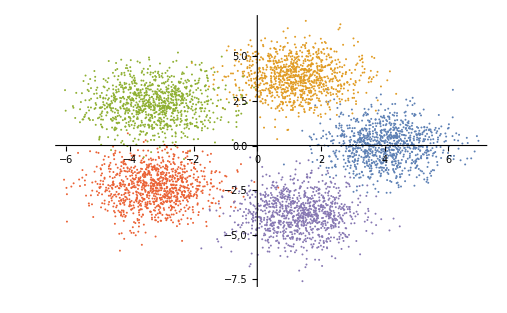

```mathematica
ListPlot[clusters,PlotTheme->"Minimal"]
```

```mathematica
net=NetChain[{
DotPlusLayer[30],
ElementwiseLayer[Ramp],
DotPlusLayer[5],
SoftmaxLayer[]
},
"Input"->{2},
"Output"->NetDecoder[{"Class",{"a","b","c","d","e"}}]
]
```

NetChain[]

```mathematica
data=Join@@MapThread[Thread[#1->#2]&,{clusters,{"a","b","c","d","e"}}];
RandomSample[data,10]//Column[#,Alignment->"→"]&
```

{0.388861,-4.78674}→e
{0.701882,-3.19679}→e
{-4.79378,-1.86371}→d
{4.43876,-0.966777}→a
{-2.80258,2.15607}→c
{-4.19054,-3.09351}→d
{0.451573,-4.37639}→e
{-3.08232,3.34639}→c
{-2.55031,-3.11902}→d
{0.701049,-2.63654}→e

```mathematica
result=NetTrain[net,data]
```

NetChain[]

```mathematica
result[{0,0}]
```

c

```mathematica
result[{0,0},"Probabilities"]
```

<|a→0.094176,b→0.119753,c→0.356704,d→0.280307,e→0.149061|>

```mathematica
Show[
Plot3D[{
result[{x,y},{"Probability","a"}],
result[{x,y},{"Probability","b"}],
result[{x,y},{"Probability","c"}],
result[{x,y},{"Probability","d"}],
result[{x,y},{"Probability","e"}]
},
{x,-6,6},{y,-6,6},
Lighting->{{"Ambient", LightBlue}},
MeshFunctions->{#3&},
Mesh->4,
PlotRange->{Full,Full,{0,1.5}}
],
ListPointPlot3D[Map[Append[#,1.3]&,clusters,{2}],PlotStyle->{Yellow,Blue,Green,Orange,Purple},
PlotRange->{Full,Full,{0,1.5}}]
]
```

-Graphics3D-

### Classification of randomly distributed data (2 dimensions) (3)

```mathematica
sample[c_,n_,d_]:=RandomVariate[MultinormalDistribution[c,d IdentityMatrix[2]],n]
```

```mathematica
sample[{0,0},10,2]
```

{{0.649905,-0.480726},{1.20291,-3.20464},{-1.24146,-3.85838},{-0.218655,-0.00955823},{-0.838317,1.77595},{-0.965031,1.72058},{0.821255,1.05836},{1.51895,2.11825},{1.43596,-2.55655},{-0.547088,0.849593}}

```mathematica
Manipulate[
clusters=sample[#,1000,d]&/@Table[radius{Cos[angle+2π n/8],Sin[angle+2π n/8]},{n,0,7}];
ListPlot[clusters,PlotTheme->"Minimal",PlotRange->{{-20,20},{-20,20}}],
{radius,1,20},
{angle,0,2π},
{d,1,4}]
```

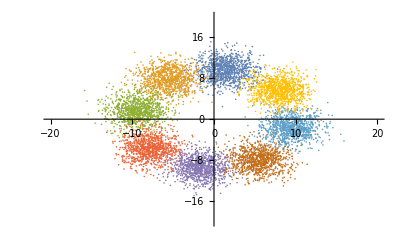

```mathematica
ListPlot[clusters,PlotTheme->"Minimal",PlotRange->{{-20,20},{-20,20}}]
```

```mathematica
Length[clusters]
```

8

```mathematica
{"a","b","c","d","e","f","g","h"}//Length
```

8

```mathematica
net=NetChain[{
DotPlusLayer[30],
ElementwiseLayer[Ramp],
DotPlusLayer[8],
SoftmaxLayer[]
},
"Input"->{2},
"Output"->NetDecoder[{"Class",{"a","b","c","d","e","f","g","h"}}]
]
```

NetChain[]

```mathematica
data=Join@@MapThread[Thread[#1->#2]&,{clusters,{"a","b","c","d","e","f","g","h"}}];
RandomSample[data,10]//Column[#,Alignment->"→"]&
```

{-5.97706,9.33595}→b
{-2.42017,-8.82445}→e
{4.07676,-10.6643}→f
{-8.73108,-0.646959}→c
{0.827444,10.162}→a
{-8.75617,6.91651}→b
{-1.66239,-10.0338}→e
{7.15464,-10.5199}→f
{-6.41608,0.964731}→c
{1.46661,-5.86717}→f

```mathematica
result=NetTrain[net,data]
```

NetChain[]

```mathematica
result[{0,0}]
```

d

```mathematica
result[{0,0},"Probabilities"]
```

<|a→0.11264,b→0.100452,c→0.0965737,d→0.200308,e→0.171501,f→0.097842,g→0.13303,h→0.0876536|>

```mathematica
Show[
Plot3D[{
result[{x,y},{"Probability","a"}],
result[{x,y},{"Probability","b"}],
result[{x,y},{"Probability","c"}],
result[{x,y},{"Probability","d"}],
result[{x,y},{"Probability","e"}],
result[{x,y},{"Probability","f"}],
result[{x,y},{"Probability","g"}],
result[{x,y},{"Probability","h"}]
},
{x,-20,20},{y,-20,20},
Lighting->{{"Ambient", LightBlue}},
MeshFunctions->{#3&},
Mesh->4,
PlotRange->{Full,Full,{0,1.5}}
],
ListPointPlot3D[Map[Append[#,1.3]&,clusters,{2}],PlotStyle->Black,
PlotRange->{Full,Full,{0,1.5}}]
]
```

-Graphics3D-

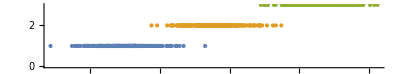

```mathematica
NumberLinePlot[clusters]
```

### Iris Dataset

```mathematica
trainingData=ExampleData[{"MachineLearning","FisherIris"},"TrainingData"];
```

```mathematica
Column[RandomSample[trainingData,5]]
```

{5.,3.,1.6,0.2}→setosa
{6.,2.2,5.,1.5}→virginica
{5.4,3.4,1.7,0.2}→setosa
{6.2,3.4,5.4,2.3}→virginica
{5.2,4.1,1.5,0.1}→setosa

```mathematica
testData=ExampleData[{"MachineLearning","FisherIris"},"TestData"];
```

```mathematica
Column[RandomSample[testData,5]]
```

{5.1,3.4,1.5,0.2}→setosa
{5.8,4.,1.2,0.2}→setosa
{6.4,2.8,5.6,2.2}→virginica
{5.4,3.,4.5,1.5}→versicolor
{4.3,3.,1.1,0.1}→setosa

```mathematica
labels=Union[Values[trainingData]]
```

{setosa,versicolor,virginica}

```mathematica
{5.1,3.4,1.5,0.2}//Length
```

4

```mathematica
net=NetChain[{
DotPlusLayer[3],
SoftmaxLayer[]
},
"Input"->4,
"Output"->NetDecoder[{"Class",labels}]
]
```

NetChain[]

```mathematica
result=NetTrain[net,trainingData]
```

NetChain[]

```mathematica
testcases=RandomSample[testData,10]
```

{{6.2,2.9,4.3,1.3}→versicolor,{4.5,2.3,1.3,0.3}→setosa,{7.1,3.,5.9,2.1}→virginica,{5.1,3.4,1.5,0.2}→setosa,{6.4,2.9,4.3,1.3}→versicolor,{5.1,3.8,1.5,0.3}→setosa,{6.3,3.3,6.,2.5}→virginica,{5.6,2.7,4.2,1.3}→versicolor,{4.6,3.4,1.4,0.3}→setosa,{6.7,3.3,5.7,2.5}→virginica}

```mathematica
Map[
<|
"expected"->Last[#],
"predicted"->result[First[#]],
"probabilities"->result[First[#],"Probabilities"]
|>&,testcases]//Dataset
```

Dataset[<>]

```mathematica
cm=ClassifierMeasurements[result,testData];
```

```mathematica
cm["Accuracy"]
```

0.933333

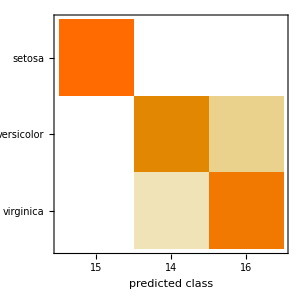

```mathematica
cm["ConfusionMatrixPlot"]
```